```mathematica
data={{9.97,-1.69},{7.65,-7},{6.81,-5.15},{7.88,-6.17},{3.06,-7.1},{8.24,-2.3},{7.96,-2.9},{7.12,-6.84},{5.95,-1.69},{9.58,-4.58},{5.94,-1},{6.68,-3.32},{5.02,-1.88},{8.26,-3.88},{4.59,-6.02},{6.57,-5.23},{9.88,-4},{10.62,-7.21},{6.83,-6.17},{5.19,-3.92},{11.81,-3.65},{9.71,-5.72},{7.41,-3.9},{7.76,-3.85},{8.34,-6.25},{3.84,-2.51},{10.78,-5.86},{9.84,-6.22},{11.42,-6.22},{8.49,-1.07}};
```

```mathematica
CovMatS = Covariance[data]
```

{{4.91093,-0.625902},{-0.625902,3.75174}}

```mathematica
MeanVector = {Mean[data [[All,1]]], Mean[data[[All,2]]]}
```

{7.77333,-4.44333}

```mathematica
MeanVector//MatrixForm
```

(7.77333
-4.44333)

```mathematica
CovMatA  = {{4.61, -0.34},{-0.34,2.85}}
```

{{4.61,-0.34},{-0.34,2.85}}

```mathematica
CovMatA//MatrixForm
```

(4.61 | -0.34
-0.34 | 2.85)

```mathematica
β = 0.89;
k = Length[data[[1]]];
n = Length[data[[All,1]]];
```

```mathematica
Xi2quantile = Quantile[ChiSquareDistribution[k], β]
```

4.41455

```mathematica
Hotellingquantile = Quantile[HotellingTSquareDistribution[k,n-1],β]
```

4.95236

```mathematica
m = {m1,m2}
```

{m1,m2}

```mathematica
Ineq1 = Expand[n*Transpose[MeanVector-m].Inverse[CovMatA].(MeanVector-m)<=Xi2quantile]
```

552.273-95.1091 m1+6.56536 m1^2+82.1975 m2+1.56647 m1 m2+10.6198 m2^2≤4.41455

```mathematica
Reduce[Ineq1, {m1,m2}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(m1==6.9497&&m2==-4.38259)||(6.9497<m1<8.59697&&5.76005×10^-16 (-6.71874×10^15-1.28042×10^14 m1)-4.7474×10^-19 √(-1.62445×10^38+4.227×10^37 m1-2.71891×10^36 m1^2)≤m2≤5.76005×10^-16 (-6.71874×10^15-1.28042×10^14 m1)+4.7474×10^-19 √(-1.62445×10^38+4.227×10^37 m1-2.71891×10^36 m1^2))||(m1==8.59697&&m2==-4.50408)

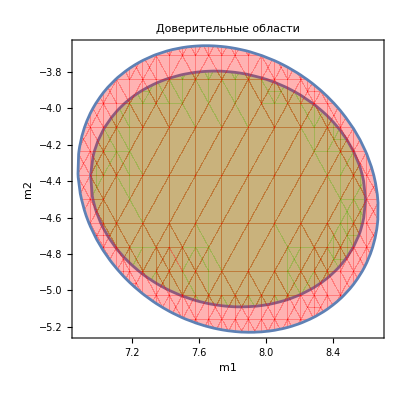

```mathematica
(*Случай а:Матрица ковариаций известна*)Ineq1=Expand[n*Transpose[MeanVector-m].Inverse[CovMatA].(MeanVector-m)<=Xi2quantile];
plot1=RegionPlot[Ineq1,{m1,6,9},{m2,-7,-2},PlotStyle->Directive[Green,Opacity[0.3]],PlotLabel->"Доверительные области"];

(*Случай б:Матрица ковариаций неизвестна*)
Ineq2=Expand[n*Transpose[MeanVector-m].Inverse[CovMatS].(MeanVector-m)<=Hotellingquantile];
plot2=RegionPlot[Ineq2,{m1,6,9},{m2,-7,-2},PlotStyle->Directive[Red,Opacity[0.3]]];

(*Объединение графиков*)
Show[plot1,plot2,PlotRange->All,FrameLabel->{"m1","m2"},PlotLegends->{"Матрица известна","Матрица неизвестна"}]
```